# EDO Logística dy/dt= r(1 - y/K)y

donde r es la tasa de crecimiento y K es la capacidad de carga, siendo r, K > 0

Referencias:

Editor:      Roberto Méndez
Created.   29 Aug 24   v2
Edited:   Feb 20 2025

Directional Field  (Slope Field) and Integral Curves

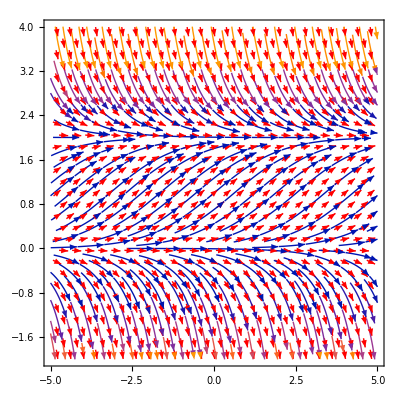

```mathematica
K = 2;
r = 1;
f[x_,y_]= r*(1 - y/K)*y;
VectorPlot[{1,f[x,y]},{x,-5,5},{y,-2,4}, VectorAspectRatio->1/4, VectorSizes->Small, 
           VectorPoints->Fine, VectorColorFunction->None, VectorStyle->Red , StreamPoints->Fine]
```

Integral Curves for IC

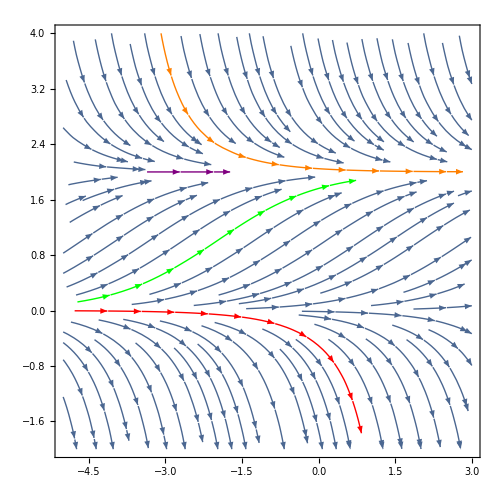

```mathematica
K = 2;
r = 1;
f[x_,y_]= r*(1 - y/K)*y;
StreamPlot[{1, f[x,y ]}, {x, -5, 3}, {y, -2, 4}, StreamColorFunction -> None, 
 StreamPoints -> {{{{-2, 2.4}, Orange}, {{-2, 2}, Purple},{{-2, 1}, Green}, 
                           {{0.5, -1}, Red}, Automatic}}, ImageSize->{500,500}]
```

Analytic Solution and plots for different values of cte C  ¿What happen here?
¿Where is the solution for y > K or y < K?
https://www.youtube.com/watch?v=Y3S_fGNFvr8

{{y[x]→(2 ⅇ^x)/(ⅇ^x+ⅇ^(2 C[1]))}}

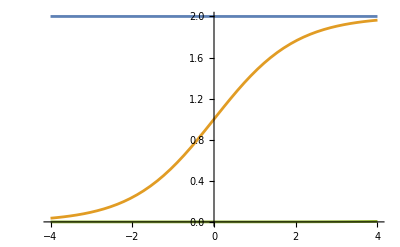

```mathematica
K = 2;
r = 1;
sol = DSolve[y'[x]== r*(1 - y[x]/K)*y[x],y[x],x]
Plot[{y[x]/. sol/. C[1]-> -100, y[x]/. sol/. C[1]-> 0 , y[x]/. sol/. C[1]-> 5},{x,-4,4}]
```

Analytic Solution with IC  ¿What happen here?
Take care with IC you select (example y[.5] = - 1 )
¿Solution 5 is correct?

{{y[x]→(6 ⅇ^(2+x))/(-1+3 ⅇ^(2+x))}}

{{y[x]→2}}

{{y[x]→(2 ⅇ^x)/(1+ⅇ^x)}}

{{y[x]→0}}

{{y[x]→(2 ⅇ^x)/(-3+ⅇ^x)}}

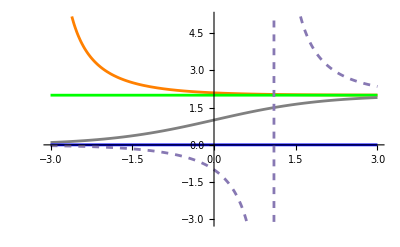

```mathematica
K = 2;
r = 1;
sol1 = DSolve[{y'[x]== r*(1 - y[x]/K)*y[x], y[-2] == 3},y[x],x]
sol2= DSolve[{y'[x]== r*(1 - y[x]/K)*y[x], y[0] == 2},y[x],x]
sol3 = DSolve[{y'[x]== r*(1 - y[x]/K)*y[x], y[0] == 1},y[x],x]
sol4 = DSolve[{y'[x]== r*(1 - y[x]/K)*y[x], y[0] == 0},y[x],x]
sol5 = DSolve[{y'[x]== r*(1 - y[x]/K)*y[x], y[0] == -1},y[x],x]
Plot[{y[x]/. sol1, y[x]/. sol2, y[x]/. sol3, y[x]/. sol4, y[x]/. sol5},{x,-3,3}, 
         PlotStyle->{Orange, Green, Gray, Blue, Dashed}]
```